```mathematica
Ellsworth[n_]:=Module[{tent=Join[Table[i,{i,n}],Table[n-i,{i,n-1}]],choices},
Graphics[Table[
choices=RandomSample[Table[j,{j,n}],tent[[i]]];
Table[Rectangle[{i,choices[[j]]}],{j,Length[choices]}]
,{i,2n-1}]
]]
EllsworthRaster[n_]:=Module[{tent=Join[Table[n-i,{i,n-1}],Table[i,{i,0,n}]],choices},
Image[SparseArray[Flatten[Table[
choices=RandomSample[Table[j,{j,n}],tent[[i]]];
Table[{choices[[j]],i}->1,{j,Length[choices]}]
,{i,2n-1}],1
]]]]
EllsworthMatrix[n_]:=Module[{tent=Join[Table[n-i,{i,n-1}],Table[i,{i,0,n}]],choices},
SparseArray[Flatten[Table[
choices=RandomSample[Table[j,{j,n}],tent[[i]]];
Table[{choices[[j]],i}->1,{j,Length[choices]}]
,{i,2n-1}],1
]]]
Componentize[m_]:=Module[{a,maxa,b,bb},
a=MorphologicalComponents[m,CornerNeighbors->False];
maxa=Max[a];
b=MorphologicalComponents[1-m,CornerNeighbors->False];
bb=Map[If[#>0,#+maxa,0]&,b,{2}];
bb+a]
SortSecond[b_]:=Sort[b,#1[[2]]>#2[[2]]&]
ComponentsByBiggest[cm_]:=SortSecond[Tally[Flatten[cm]]]
ComponentSelect[cm_,c_]:=Map[If[#==c,1,0]&,cm,{2}]
ComponentRelabel[cm_,in_,out_]:=Map[If[#==in,out,#]&,cm,{2}]
BoundaryWalk[component_,LR_]:=Block[{$RecursionLimit=Infinity},Module[{dimx,dimy,x,y,lst,h,dir},
lst=h[];
{dimy,dimx}=Dimensions[component];
y=dimy;
dir={0,-1}; (*direction we're moving*)
x=Position[component[[dimy,All]],1][[LR,1]]; (* LR =1, left, LR=-1, right *)
If[LR==-1,x=x+1];
lst=h[{x,y},lst]; (* linked list*)
{x,y}={x,y}+dir;
lst=h[{x,y},lst];
While[y≥1,(* stop when we hit top *)
(* always keep 1 on the right (if LR = +1)*)
(* case analysis for dir? *)
dir=If[LR==1,
Switch[dir,
{0,-1},
If[component[[y,x]]==1,
If[x≠1&&component[[y,x-1]]==1,
{-1,0},
{0,-1}
],
{+1,0}
],
{-1,0},
If[x≠1&&component[[y,x-1]]==1,
If[(*y≠dimy&&*)component[[y+1,x-1]]==1,
{0,1},
{-1,0}
],
{0,-1}
],
{0,+1},
If[(*y≠1&&*)component[[y+1,x-1]]==1,
If[component[[y+1,x]]==1,
{+1,0},
{0,+1}
],
{-1,0}
],
{+1,0},
If[component[[y+1,x]]==1,
If[component[[y,x]]==1,
{0,-1},
{+1,0}
],
{0,+1}
]
]
,
(* LR=-1*)
Switch[dir,
{0,-1},
If[component[[y,x-1]]==1,
If[x≤dimx&&component[[y,x]]==1,
{1,0},
{0,-1}
],
{-1,0}
],
{-1,0},
If[component[[y+1,x-1]]==1,
If[component[[y,x-1]]==1,
{0,-1},
{-1,0}
],
{0,+1}
],
{0,+1},
If[component[[y+1,x]]==1,
If[component[[y+1,x-1]]==1,
{-1,0},
{0,+1}
],
{+1,0}
],
{+1,0},
If[x≤dimx&&component[[y,x]]==1,
If[component[[y+1,x]]==1,
{0,+1},
{+1,0}
],
{0,-1}
]
]
];
{x,y}={x,y}+dir;
lst=h[{x,y},lst];
];
Partition[Flatten[lst/.h->List],2]
]]
DrawBWLineOld[bw_]:=Graphics[Line[Table[{bw[[i,1]],-bw[[i,2]]},{i,Length[bw]}]]]
DrawBWLine[bw_]:=Module[{lbw=Length[bw],curvy,dir},
curvy=Partition[Flatten[Table[
dir=bw[[i]]-bw[[i+1]];
{bw[[i+1]]+1/4 dir,bw[[i]]-1/4 dir}
,{i,lbw-1,1,-1}]],2];
Graphics[Line[Table[{curvy[[i,1]],-curvy[[i,2]]},{i,Length[curvy]}]]]]
```

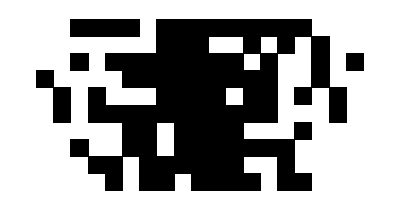
{0.000487,-Graphics-}

```mathematica
Timing[Ellsworth[10]]
```

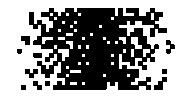
{0.001407,-Graphics-}

```mathematica
Timing[Ellsworth[20]]
```

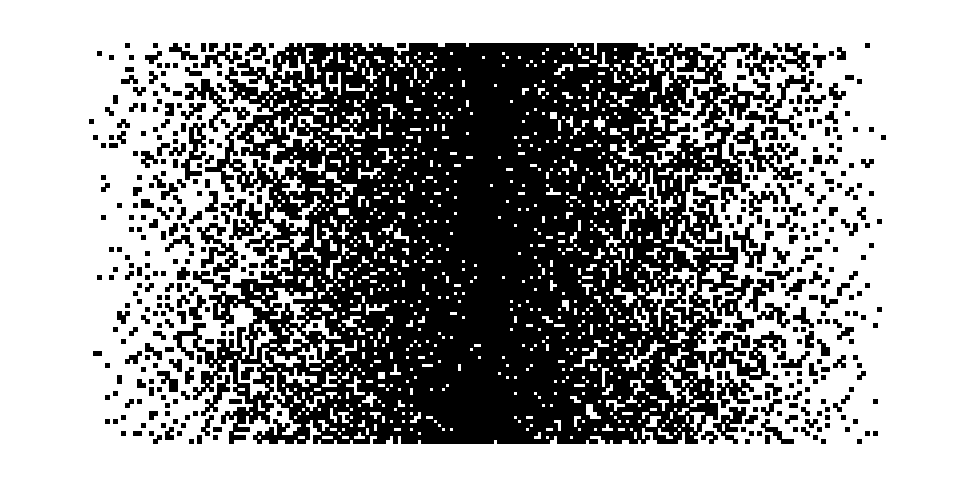
{0.024379,-Graphics-}

```mathematica
Timing[Ellsworth[100]]
```

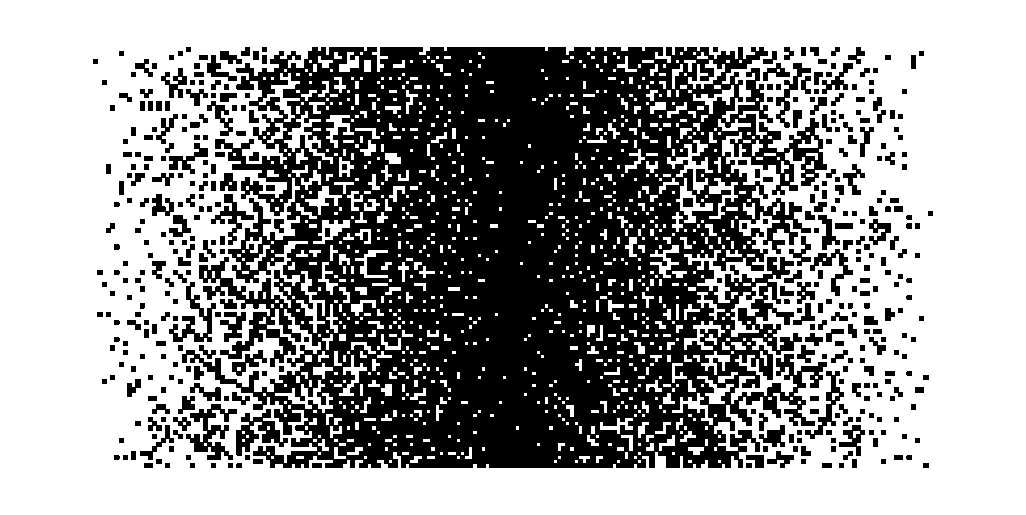
{0.019079,-Graphics-}

```mathematica
Timing[Ellsworth[100]]
```

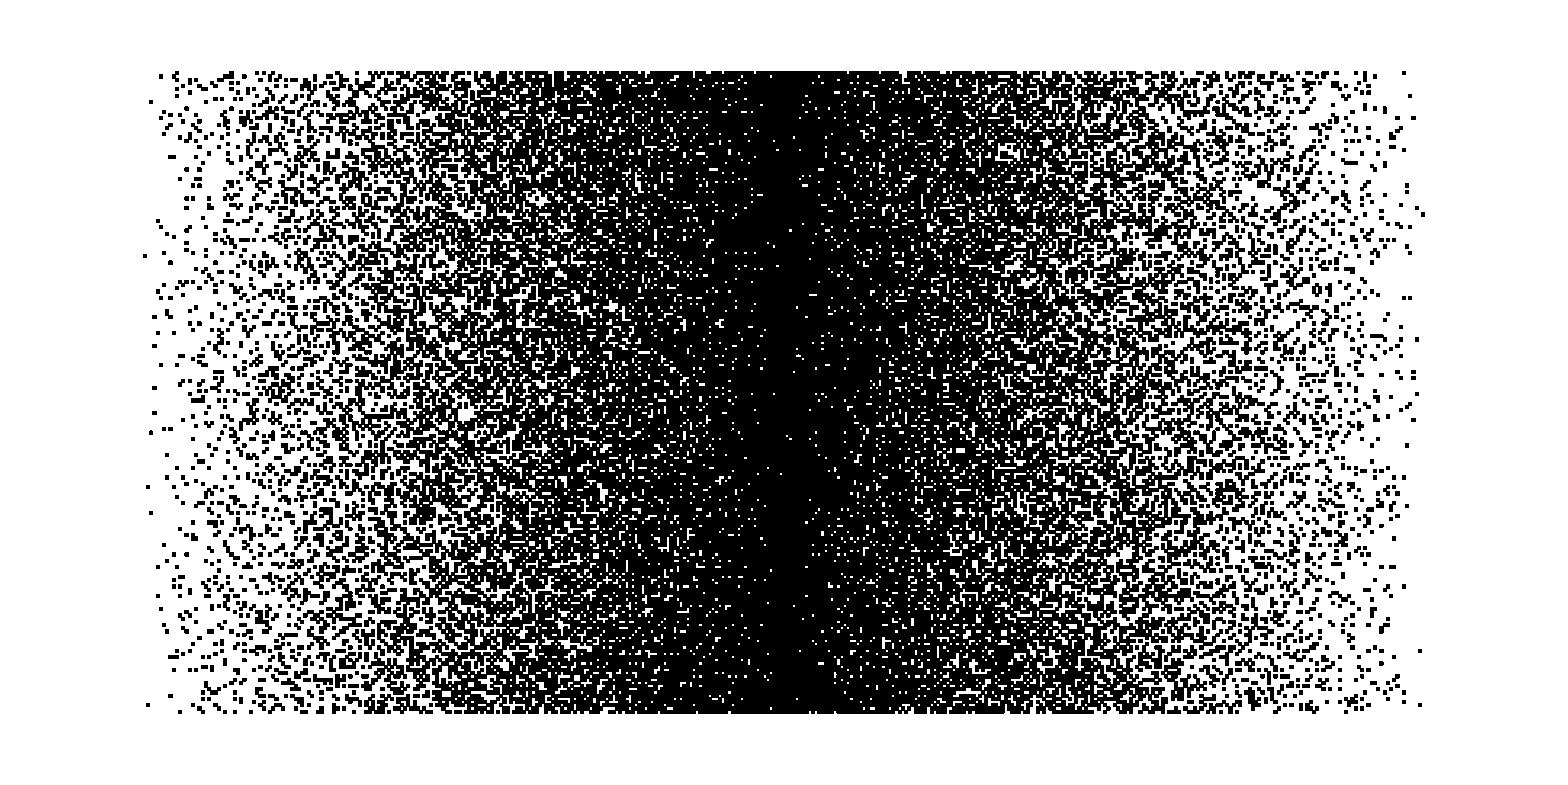

```mathematica
Ellsworth[200]
```

```mathematica
n=41;
data2=Join[Table[Range[n-i],{i,n}],Table[Range[i],{i,n}]];
(*data2=Join[Table[Range[n-i],{i,n}],Table[Range[n+1-i,n],{i,n}]];*)
notseine=SparseArray[Flatten[Table[
choices=data2[[i]];
Table[{choices[[j]],i}->1,{j,Length[choices]}]
,{i,Length[data]}],1
]];
nnotseine=Normal[notseine];
Image[nnotseine]
```

-Graphics-

-Graphics-

```mathematica
n=41;
data={Join[Range[20],Range[22,n]],
Join[Range[29],Range[31,37],Range[39,n]],
Join[Range[22],Range[24,26],{28},Range[30,n]],
Join[Range[13],{15,16},{18},{20,21},Range[23,n]],
Join[Range[8],Range[10,18],{20},Range[22,25],{27},Range[29,n]],
Join[Range[4],Range[6,18],{21,22},Range[24,27],Range[30,n]],
Join[{1},{3,4},Range[6,12],{14},{16,17},Range[19,35],Range[37,40]],
Join[{1},Range[4,14],Range[18,27],Range[29,33],Range[35,38],Range[40,n]],
Join[{1},Range[4,6],{8,9},Range[11,22],Range[24,27],{30,31},{33,34,35},Range[37,n]],
Join[Range[6],{8},{10,11},Range[14,19],{21,22},{25},{27,28},Range[31,n]],
Join[Range[4],{6},Range[8,13],Range[15,19],{21},{23,24},Range[27,35],{37},{39}],
Join[{2},Range[7,10],{12},{14,15},{17},Range[19,23],{25},Range[27,39],{n}],
Join[{1},{4,5},Range[7,11],Range[13,17],{19},{25,26},{28,29,30},{32},Range[34,n]],
Join[Range[7],{12,13},{16},{18,19},{21},{23,24},{26,27},{29,30},Range[32,35],{37,38,39},{n}],
Join[Range[3],{5},{7},Range[12,15],{18,19},{21,22,23},{25},{27},{29,30,31},Range[33,37],{39},{n}],
Join[{2,3},{6,7,8},{11,12},{18},{21},{23},{25},Range[27,38],{40,n}],
Join[{2},{5,6},Range[8,16],{20,21},{23,24},{26},{29},{31},{35,36},{38,39,40}],
Join[{2},{4},Range[7,12],Range[14,17],Range[25,27],Range[30,34],{37,38},{n}],
Join[{1},{3,4,5},{7,8},{13},{15,16,17},{19,20,21},{23},{25},{27},{31},{34,35,36},{40,n}],
Join[{2},{5,6},{10,11,12},{15,16},{18,19},{22},{24},{26},{30,31,32,33},{35,36,37,38}],
Join[Range[3],{6,7},{12},{14,15},{18,19,20},{25},{27,28,29,30},{32},{34,35},{38}],
Join[{1,2},{4},{6},{8,9,10},{13},{17},{21},{25,26,27},{32,33},Range[38,n]],
Join[{2,3,4,5},{9},{14},{17,18},{21,22},{25},{27,28},{32},{36,37},{39},{n}],
Join[{1},{3,4},{8,9,10},{12,13},{16},{20,21},{24},{27},{29},{32},{36},{40}],
Join[{1,2},Range[4,8],{12},{23,24,25,26},{29,30},{35},{37}],
Join[{2,3},{9,10},{12},{15},{18,19,20},{28},{32},{35},{37,38},{n}],
Join[{9,10,11,12,13},{15},{18},{24},{26,27},{30},{35},{37},{40}],
Join[{3,4},{8},{10},{13,14},{16,17},{23},{29,30},{32,33}],
Join[{1},{3},{5,6},{8,9},{18},{20},{23},{30},{34},{39}],
Join[{1},{3},{6},{9},{18},{20},{23},{26},{37},{39},{n}],
Join[{2},{4},{7,8},{10},{13},{17},{31},{33},{39}],
Join[{1},{7},{17},{20},{26},{33},{36},{38},{n}],
Join[{4,5},{9},{13},{18},{33},{37},{40}],
Join[{1},{9},{18},{25},{32},{39,40}],
Join[{2},{5},{27},{34,35,36}],
Join[{3},{11},{18},{28},{31}],
Join[{11},{15},{30},{38}],
Join[{17},{21},{30}],
Join[{8},{36}],
Join[{34}],
{},
{8},
Join[{22},{35}],
Join[{1},{16},{25}],
Join[{8},{21,22},{28}],
Join[{8},{19},{28},{30},{33}],
Join[{7},{19},{22},{31},{36},{38}],
Join[{17},{19},{21},{23,24},{30},{36}],
Join[{10},{14},{16},{20},{24},{29},{32,33},{36}], (* the 36 should be in next column! *)
Join[{1},{6},{9,10,11,12},{14},{17}],
Join[{7},{9},{13},{17},{19},{24},{26},{33},{38},{40}],
Join[{5},{8},{11},{13,14},{16,17},{25},{36},{38,39}],
Join[{1,2},{6,7},{11},{16},{22},{26},{28,29},{32},{n}],
Join[{1},{5},{12},{17,18},{20,21},{23,24},{26},{28,29},{34}],
Join[{4,5,6},{10},{14,15},{20},{22,23,24},{29},{37},{39},{n}],
Join[{3,4,5,6},{11},{21},{23},{28},{31,32,33,34},{37},{39,40}],
Join[{3},{8,9,10},{14,15,16,17},{20,21,22},{24},{29},{33},{36},{38}],
Join[{2},{4},{9},{13},{16},{18,19,20},{23},{26},{29,30,31,32,33},{39,40}],
Join[{2},Range[4,10],{14,15},{20},{25},{27},{33},{35},{37,38},{n}],
Join[{5,6},{8},{10,11},{13},{17},{19,20,21},{24},{28,29},{31},{36,37},Range[39,n]],
Join[{1},{3},{5},{8},{10},{13},{15,16},{19},{24,25,26},{28},{30},{34,35},Range[38,n]],
Join[{2,3},{8},{10},Range[13,18],{21,22},{24},{26,27},{29},{32},{35,36,37},{39}],
Join[{2},{4,5,6},{9},{11},{13},{15},{17,18},Range[22,25],Range[27,30],{33},{36},{38},{40}],
Join[{3},{10},{12},{14},{17},{19},{21,22},Range[24,31],{33},Range[35,38],{40,n}],
Join[{2},{4,5},{8},{10},{13,14,15},{19,20,21},{23,24},{26},Range[29,35],{37,38,39}],
Join[{1},{3,4},{6},{8},{11},{13,14},{16,17},{19,20},{22,23},{25,26},{28,29},{31},{33,34,35},{38},{40,n}],
Join[{2},{4},{7},{9},Range[11,16],Range[20,23],{25,26,27},Range[31,34],Range[36,39],{n}],
Join[{2,3},Range[6,9],{11,12},Range[14,17],{19,20},{22},{25,26},{29,30,31},{33},{35,36,37},{39},{n}] (* needs one more...? *),
Join[{2},{4},{6,7},{9,10},Range[12,17],Range[21,24],Range[26,29],{31},{33},Range[35,39],{n}],
Join[Range[6],Range[8,11],Range[14,19],{21,22},{24},{27,28,29},Range[35,n]],
Join[Range[8],Range[10,19],Range[22,25],{27,28},{31,32},{34},{36},{38,39}],
Join[Range[5],Range[7,9],Range[11,13],Range[15,19],Range[22,30],{32},{35,36},{38,39},{n}],
Join[{1},{3},{5},Range[7,13],{15,16},Range[18,25],{27,28},Range[30,36],{38},{40,n}],
Join[{1},Range[3,11],{13,14},Range[16,23],Range[26,30],{32},{34,35},Range[37,n]],
Join[Range[8],{10,11},Range[13,21],{23},{25,26,27},{29,30,31},{33,34},Range[36,n]],
Join[Range[3],{5,6},Range[8,30],{32,33},{35,36},{38,39},{n}],
Join[{1},Range[3,17],{19,20,21},Range[23,34],{36,37,38},{40,n}],
Join[Range[16],Range[18,29],{31,32,33},Range[35,40]],
Join[Range[11],Range[13,27],Range[29,38],{40,n}],
Join[Range[4],Range[6,31],Range[33,n]],
Join[Range[34],Range[36,n]]
};
seine=SparseArray[Flatten[Table[
choices=data[[i]];
Table[{choices[[j]],i}->1,{j,Length[choices]}]
,{i,Length[data]}],1
]]
```

SparseArray[<1639>,{41,81}]

```mathematica
nseine=Normal[seine];
```

```mathematica
Total[nseine]
Image[nseine]
```

{40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,0,1,2,3,4,5,6,7,9,8,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,26,28,29,30,31,32,33,34,35,36,37,38,39,40}

```mathematica
N[Exp[Total[Table[Log[Binomial[41,i]],{i,41}]]],5]
```

4.4477×10^332

```mathematica
%^2
```

1.978×10^665

```mathematica
81*42
```

3402

```mathematica
cseine=Componentize[nseine];
cseine//Colorize
cbseine=ComponentsByBiggest[cseine];
{cmseine1,cmseine2,cmseine3}=cbseine[[1;;3,1]];
ComponentRelabel[ComponentRelabel[ComponentRelabel[ComponentRelabel[ComponentRelabel[cseine,cmseine1,0],4,-3],cmseine2,4],cmseine3,4],-3,cmseine1]//Colorize
```

-Graphics-

-Graphics-

```mathematica
Image[cseine3]
```

-Graphics-

-Graphics-

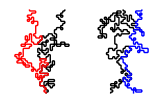

```mathematica
cseine1=ComponentSelect[cseine,cmseine1];
Image[cseine1]
bwR1=BoundaryWalk[cseine1,1];
bwL1=BoundaryWalk[cseine1,-1];
cseine2=ComponentSelect[cseine,cmseine2];
bwR2=BoundaryWalk[cseine2,1];
bwL2=BoundaryWalk[cseine2,-1];
cseine3=ComponentSelect[cseine,cmseine3];
bwR3=BoundaryWalk[cseine3,1];
bwL3=BoundaryWalk[cseine3,-1];
Show[DrawBWLine[bwL1],DrawBWLine[bwR1],Graphics[Red],DrawBWLine[bwL2],Graphics[Blue],DrawBWLine[bwR3]]
```

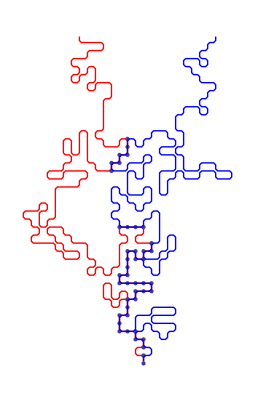

```mathematica
bwintersect12=Intersection[bwL2,bwR1];
f12=Show[Graphics[Red],DrawBWLine[bwL2],ListPlot[Table[{bwintersect12[[i,1]],-bwintersect12[[i,2]]},{i,Length[bwintersect12]}]],Graphics[Blue],DrawBWLine[bwR1]]
```

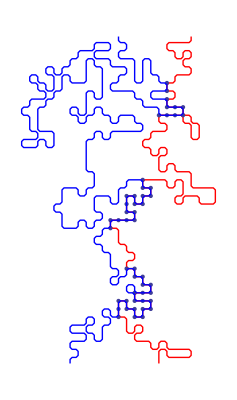

```mathematica
bwintersect13=Intersection[bwR3,bwL1];
f13=Show[Graphics[Red],DrawBWLine[bwR3],ListPlot[Table[{bwintersect13[[i,1]],-bwintersect13[[i,2]]},{i,Length[bwintersect13]}]],Graphics[Blue],DrawBWLine[bwL1]]
```

```mathematica
N[Mean[bwL1]]
N[Mean[bwR3]]
N[Mean[bwR1]]
N[Mean[bwL2]]
```

{58.6174,16.2315}

{66.2963,20.9198}

{26.0578,21.2089}

{17.7067,21.1971}

```mathematica
.5944*41
(1-.5944)*41
1.5944*41
(2-.5944)*41
```

24.3704

16.6296

65.3704

57.6296

```mathematica
bwL1
```

{{61,0},{61,1},{62,1},{62,2},{61,2},{61,3},{62,3},{63,3},{63,4},{63,5},{63,6},{64,6},{64,5},{64,4},{64,3},{65,3},{65,4},{65,5},{66,5},{66,6},{67,6},{67,7},{66,7},{65,7},{65,8},{66,8},{67,8},{67,9},{68,9},{69,9},{69,10},{68,10},{67,10},{66,10},{66,9},{65,9},{64,9},{64,8},{63,8},{63,7},{62,7},{61,7},{60,7},{60,6},{61,6},{61,5},{62,5},{62,4},{61,4},{60,4},{60,3},{59,3},{58,3},{58,2},{59,2},{60,2},{60,1},{59,1},{58,1},{58,2},{57,2},{56,2},{56,3},{55,3},{55,4},{54,4},{54,5},{53,5},{53,4},{52,4},{52,5},{53,5},{53,6},{53,7},{52,7},{52,6},{51,6},{51,5},{50,5},{50,6},{51,6},{51,7},{52,7},{52,8},{51,8},{50,8},{50,9},{49,9},{49,10},{50,10},{50,11},{50,12},{51,12},{51,13},{50,13},{49,13},{49,14},{50,14},{51,14},{51,13},{52,13},{52,14},{53,14},{53,13},{53,12},{52,12},{51,12},{51,11},{51,10},{51,9},{52,9},{52,8},{53,8},{53,7},{54,7},{54,6},{54,5},{55,5},{55,6},{56,6},{57,6},{57,5},{57,4},{57,3},{58,3},{58,4},{59,4},{59,5},{59,6},{59,7},{59,8},{58,8},{58,7},{57,7},{57,8},{57,9},{57,10},{56,10},{56,9},{55,9},{55,10},{56,10},{56,11},{57,11},{57,10},{58,10},{58,9},{59,9},{59,10},{60,10},{60,11},{61,11},{61,10},{62,10},{63,10},{63,11},{64,11},{64,12},{63,12},{62,12},{61,12},{60,12},{60,13},{59,13},{59,12},{58,12},{58,13},{57,13},{57,14},{57,15},{57,16},{57,17},{58,17},{58,18},{58,19},{57,19},{57,20},{56,20},{56,19},{55,19},{54,19},{54,20},{54,21},{53,21},{53,22},{54,22},{54,23},{54,24},{55,24},{56,24},{56,23},{57,23},{57,24},{58,24},{58,23},{59,23},{59,22},{58,22},{58,21},{58,20},{59,20},{60,20},{60,21},{61,21},{61,20},{61,19},{62,19},{62,18},{63,18},{64,18},{64,19},{65,19},{65,20},{64,20},{64,21},{63,21},{63,20},{62,20},{62,21},{62,22},{63,22},{63,23},{62,23},{61,23},{60,23},{60,24},{59,24},{59,25},{58,25},{58,26},{59,26},{59,27},{60,27},{60,28},{60,29},{61,29},{61,30},{60,30},{60,31},{61,31},{61,30},{62,30},{62,29},{63,29},{63,30},{64,30},{64,31},{65,31},{65,32},{64,32},{63,32},{63,31},{62,31},{62,32},{63,32},{63,33},{64,33},{65,33},{65,34},{64,34},{64,35},{63,35},{63,34},{62,34},{62,33},{61,33},{61,34},{61,35},{60,35},{60,34},{59,34},{59,35},{60,35},{60,36},{59,36},{59,37},{59,38},{58,38},{58,37},{57,37},{57,36},{58,36},{58,35},{57,35},{57,36},{56,36},{55,36},{55,37},{56,37},{57,37},{57,38},{56,38},{55,38},{55,39},{56,39},{56,40},{55,40},{55,41}}

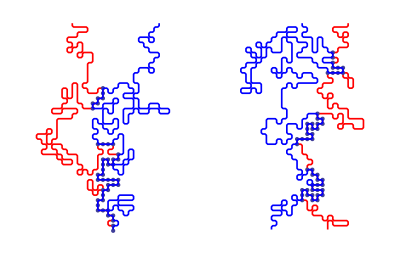

```mathematica
Show[Graphics[Thickness[.003]],f13,f12]
```

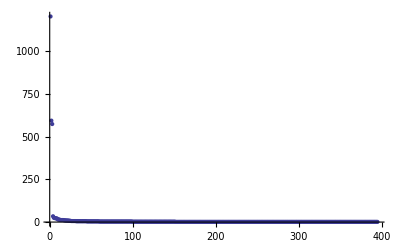

```mathematica
ListPlot[ComponentsByBiggest[cseine][[All,2]],PlotRange->All]
```

```mathematica
Timing[EllsworthRaster[100]]
```

{0.04114,-Graphics-}

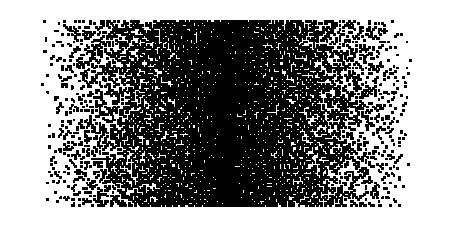
{0.019229,-Graphics-}

```mathematica
Timing[Ellsworth[100]]
```

```mathematica
Timing[Export["ellsworth6.png",EllsworthRaster[41]]]
```

{0.059627,ellsworth6.png}

```mathematica
m={{0,1,1,0,0},{0,1,1,1,1},{0,0,1,1,1},{1,0,0,0,0},{0,0,1,0,1}};
```

```mathematica
myBwlabel[mat_?MatrixQ]:=Module[{clus},clus=DeleteCases[Flatten[Outer[(With[{x=Total[Abs[#1-#2]]},Switch[x,0,{#1},1,{#1,#2},_,Null]]&),Position[mat,1],Position[mat,1],1],1],Null]//.{left___,p1:{l1___,x_List,r1___},mid___,p2:{l2___,x_List,r2___},right___}:>{left,Union[p1,p2],mid,right};
Print[clus];
Normal[SparseArray[Flatten[MapThread[Function[{x,y},Map[Rule[#,y]&,x]],{clus,Range[Length[clus]]},1],1],Dimensions[mat]]]]
```

```mathematica
(4/5)/1.1/2
```

0.363636

```mathematica
16.5/45.25
```

0.364641

```mathematica
myBwlabel[m]
```

{{{1,2},{1,3},{2,2},{2,3},{2,4},{2,5},{3,3},{3,4},{3,5}},{{4,1}},{{5,3}},{{5,5}}}

{{0,1,1,0,0},{0,1,1,1,1},{0,0,1,1,1},{2,0,0,0,0},{0,0,3,0,4}}

```mathematica
Dimensions[m]
```

{42,83}

```mathematica
m[[All,41;;43]]//Colorize
```

-Graphics-

```mathematica
MatrixForm[%]
```

(0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
2 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 4)

```mathematica
m=Normal[EllsworthMatrix[42]];
```

```mathematica
Max[MorphologicalComponents[m,CornerNeighbors->False]]
```

210

```mathematica
MorphologicalComponents[m,CornerNeighbors->False]//Colorize
MorphologicalComponents[1-m,CornerNeighbors->False]//Colorize
MorphologicalComponents[m,CornerNeighbors->False]+
1000MorphologicalComponents[1-m,CornerNeighbors->False]//Colorize
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
mm=EllsworthMatrix[100];
```

```mathematica
a=MorphologicalComponents[mm,CornerNeighbors->False];
maxa=Max[a];
b=MorphologicalComponents[1-mm,CornerNeighbors->False];
a+b+maxa//Colorize
```

-Graphics-

```mathematica
bb=Map[If[#>0,#+maxa,0]&,b,{2}];
```

```mathematica
Dimensions[bb]
```

{100,199}

```mathematica
Dimensions[b]
```

{100,199}

```mathematica
bb+a//Colorize
```

-Graphics-

```mathematica
Max[bb+a]
```

2209

```mathematica
mm2=EllsworthMatrix[15];
cm2=Componentize[mm2];
cm2//Colorize
```

-Graphics-

```mathematica
cm=Componentize[m];
cm//Colorize
```

-Graphics-

```mathematica
mm20=EllsworthMatrix[10];
cm20=Componentize[mm20];
cm20//Colorize
{cmc1,cmc2,cmc3}=ComponentsByBiggest[cm20][[1;;3,1]];
```

-Graphics-

```mathematica
black20=ComponentSelect[cm20,cmc1];
```

```mathematica
Image[black20]
```

-Graphics-

```mathematica
Dimensions[black20]
```

{10,19}

```mathematica
bw20
```

{{16,0},{16,1},{16,2},{17,2},{17,3},{17,4},{16,4},{15,4},{14,4},{14,3},{13,3},{13,2},{12,2},{12,3},{13,3},{13,4},{14,4},{14,5},{15,5},{15,6},{14,6},{14,7},{15,7},{15,8},{16,8},{16,9},{15,9},{14,9},{14,8},{13,8},{12,8},{12,9},{13,9},{14,9},{14,10}}

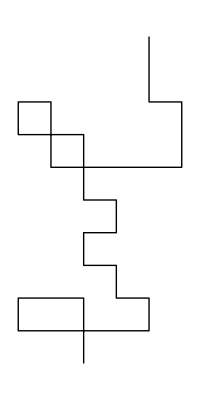

```mathematica
bw20=BoundaryWalk[black20,-1];
```

```mathematica
WalkMatrix[walk_,{dimy_,dimx_}]:=Module[{len=Length[walk]},Normal[SparseArray[Table[walk[[i,All]]->1,{i,len}],{dimy,dimx}]]]
```

```mathematica
WalkMatrix[BoundaryWalk[black20,1],Dimensions[black20]]
```

SparseArray::posd: The left-hand side of {5, 0} → 1 in {{5, 0} → 1, {5, 1} → 1, {5, 2} → 1, {5, 3} → 1, {4, 3} → 1, {4, 4} → 1, {3, 4} → 1, {3, 5} → 1, {4, 5} → 1, {5, 5} → 1, {5, 4} → 1, {6, 4} → 1, {6, 3} → 1, {7, 3} → 1, {7, 2} → 1, {6, 2} → 1, {6, 1} → 1, {7, 1} → 1, {7, 2} → 1, {8, 2} → 1, {8, 3} → 1, {7, 3} → 1, {7, 4} → 1, {7, 5} → 1, {6, 5} → 1, {6, 6} → 1, {7, 6} → 1, {8, 6} → 1, {9, 6} → 1, {9, 7} → 1, {8, 7} → 1, {7, 7} → 1, {6, 7} → 1, {6, 8} → 1, {6, 9} → 1, {5, 9} → 1, {4, 9} → 1, {3, 9} → 1, {3, 10} → 1} is not a position or a pattern that will match the position of an element in an array with dimensions {10, 19}.

SparseArray[{{5,0}→1,{5,1}→1,{5,2}→1,{5,3}→1,{4,3}→1,{4,4}→1,{3,4}→1,{3,5}→1,{4,5}→1,{5,5}→1,{5,4}→1,{6,4}→1,{6,3}→1,{7,3}→1,{7,2}→1,{6,2}→1,{6,1}→1,{7,1}→1,{7,2}→1,{8,2}→1,{8,3}→1,{7,3}→1,{7,4}→1,{7,5}→1,{6,5}→1,{6,6}→1,{7,6}→1,{8,6}→1,{9,6}→1,{9,7}→1,{8,7}→1,{7,7}→1,{6,7}→1,{6,8}→1,{6,9}→1,{5,9}→1,{4,9}→1,{3,9}→1,{3,10}→1},{10,19}]

```mathematica
Position[a,d]
```

{{2},{3}}

```mathematica
a={b,d,d};
a[[-1]]
```

d

```mathematica
perim20=MorphologicalComponents[MorphologicalPerimeter[black20,CornerNeighbors->False],CornerNeighbors->False];
```

```mathematica
Image[perim20]
```

-Graphics-

```mathematica
{p1,p2}=ComponentsByBiggest[perim200][[2;;3,1]];
```

{{0,1662754},{105146,255},{110499,243},{39974,233},{64874,222},{10020,215},{72102,206},{97390,189},{82924,185},{27390,181},{65883,175},{34828,161},{109041,159},{91446,157},{72574,156},{8381,156},{43606,152},{114521,151},{65104,151},{86424,149},{73417,145},{38428,144},{54786,143},«114503»,{85,1},{82,1},{81,1},{80,1},{75,1},{73,1},{71,1},{70,1},{69,1},{68,1},{65,1},{63,1},{62,1},{61,1},{59,1},{56,1},{55,1},{48,1},{45,1},{39,1},{17,1},{15,1},{8,1}}

```mathematica
(*cseine=Componentize[nseine];
cseine//Colorize
cbseine=ComponentsByBiggest[cseine];
{cmseine1,cmseine2,cmseine3}=cbseine[[1;;3,1]];*)
PlotBoundaries[cseine_,{cmseine1_,cmseine2_,cmseine3_}]:=Module[{cseine1,cseine2,cseine3,bw100R1,bw100L1,bw100R2,bw100L2,bw100R3,bw100L3,bw100intersect12,f10012,f10013,bw100intersect13},
cseine1=ComponentSelect[cseine,cmseine1];
bw100R1=BoundaryWalk[cseine1,1];
bw100L1=BoundaryWalk[cseine1,-1];
cseine2=ComponentSelect[cseine,cmseine2];
bw100R2=BoundaryWalk[cseine2,1];
bw100L2=BoundaryWalk[cseine2,-1];
cseine3=ComponentSelect[cseine,cmseine3];
bw100R3=BoundaryWalk[cseine3,1];
bw100L3=BoundaryWalk[cseine3,-1];
bw100intersect12=Intersection[bw100L2,bw100R1];
f10012=Show[Graphics[Red],If[Length[bw100L2]>Length[bw100R2],DrawBWLine[bw100L2],DrawBWLine[bw100R2]],If[Length[bw100intersect12]>0,ListPlot[Table[{bw100intersect12[[i,1]],-bw100intersect12[[i,2]]},{i,Length[bw100intersect12]}]],{}],Graphics[Blue],DrawBWLine[bw100R1]];
bw100intersect13=Intersection[bw100R3,bw100L1];
f10013=Show[Graphics[Red],If[Length[bw100R3]>Length[bw100L3],DrawBWLine[bw100R3],DrawBWLine[bw100L3]],If[Length[bw100intersect13]>0,ListPlot[Table[{bw100intersect13[[i,1]],-bw100intersect13[[i,2]]},{i,Length[bw100intersect13]}]],{}],Graphics[Blue],DrawBWLine[bw100L1]];
Show[f10013,f10012]]
```

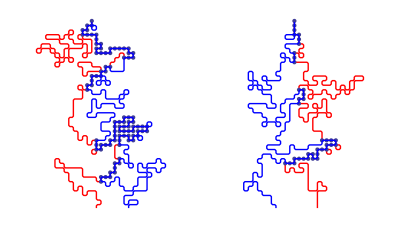

```mathematica
Show[Graphics[Thick],PlotBoundaries[cm200,{cmc1,cmc2,cmc3}]]
```

```mathematica
h200=ComponentRelabel[ComponentRelabel[ComponentRelabel[ComponentRelabel[ComponentRelabel[cm200,cmc1,0],4,-3],cmc2,4],cmc3,4],-3,cmc1];
Colorize[h200]
```

-Graphics-

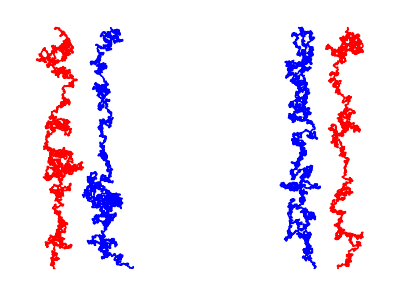

```mathematica
500
```

```mathematica
distributnumcomps=Table[mm200=EllsworthMatrix[41];
(*Image[mm200]*)
cm200=Componentize[mm200];
(*cm200//Colorize*)
cbb200=ComponentsByBiggest[cm200];
Length[cbb200],{2500}];
(*{cmc1,cmc2,cmc3}=cbb200[[1;;3,1]];
ComponentSelect[cm200,cmc1]//Image
ComponentSelect[cm200,cmc2]//Image
ComponentSelect[cm200,cmc3]//Image*)
```

```mathematica
N[Mean[distributnumcomps]]
```

383.277

```mathematica
N[Variance[distributnumcomps]]
```

244.027

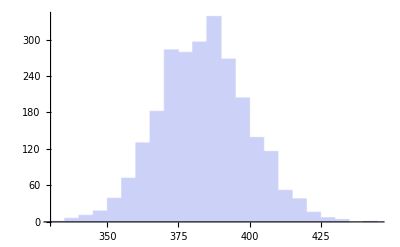

```mathematica
Histogram[distributnumcomps]
```

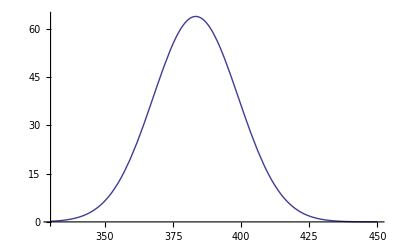

```mathematica
Plot[2500PDF[NormalDistribution[383.3,√244.03],x],{x,330,450}]
```

```mathematica
√244.03
```

15.6215

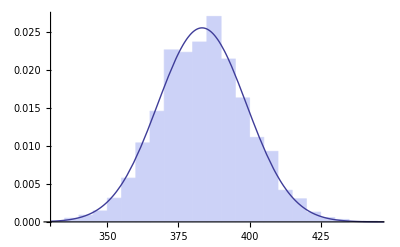

```mathematica
Show[Histogram[distributnumcomps,Automatic,"PDF"],Plot[PDF[NormalDistribution[383.3,√244.03],x],{x,330,450}]]
```

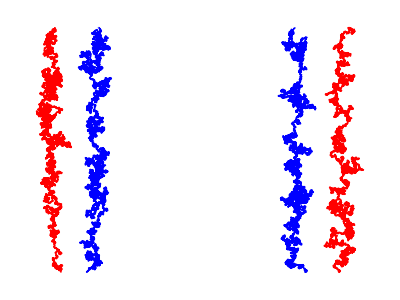

```mathematica
1000
```

```mathematica
h200=ComponentRelabel[ComponentRelabel[ComponentRelabel[ComponentRelabel[ComponentRelabel[cm200,cmc1,0],4,-3],cmc2,4],cmc3,4],-3,cmc1];
```

```mathematica
Colorize[h200]
```

-Graphics-

```mathematica
Image[mm200]
```

-Graphics-

```mathematica
mm200=EllsworthMatrix[1000];
cm200=Componentize[mm200];
cm200//Colorize
{cmc1,cmc2,cmc3}=ComponentsByBiggest[cm200][[1;;3,1]];
ComponentSelect[cm200,cmc1]//Image
ComponentSelect[cm200,cmc2]//Image
ComponentSelect[cm200,cmc3]//Image
```

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

```mathematica
ListPlot[ComponentsByBiggest[cm200][[All,2]],PlotRange->All]
```

-Graphics-

```mathematica
cb200=ComponentsByBiggest[cm200];
```

```mathematica
Tally[cb200[[All,2]]]
```

{{656585,1},{329421,1},{326540,1},{1444,1},{1126,1},{1120,1},{1033,1},{884,1},{838,1},{815,1},{737,1},{736,1},{706,1},{704,1},{685,1},{684,1},{673,1},{624,1},{612,1},{600,1},{572,1},{569,1},{566,1},{543,1},{521,1},{520,1},{508,1},{503,1},{502,1},{495,1},{471,1},{461,1},{455,1},{443,1},{439,1},{438,3},{437,1},{430,1},{426,1},{397,1},{384,1},{383,1},{371,1},{368,1},{366,1},{364,1},{358,1},{355,1},{345,1},{336,1},{334,1},{332,1},{329,1},{328,1},{321,1},{318,1},{315,1},{313,1},{312,1},{311,1},{310,1},{304,1},{302,1},{299,1},{293,1},{290,1},{287,2},{286,1},{283,1},{274,1},{263,2},{256,1},{255,1},{253,1},{252,1},{251,1},{248,1},{247,1},{246,1},{243,1},{241,1},{239,1},{238,1},{237,1},{236,1},{235,1},{231,2},{226,1},{225,2},{223,1},{221,1},{220,1},{219,2},{215,1},{214,1},{212,1},{211,1},{210,1},{209,1},{208,1},{206,1},{205,1},{204,3},{203,2},{202,1},{201,1},{200,1},{198,1},{197,2},{196,3},{195,1},{194,2},{193,1},{190,2},{187,1},{186,1},{185,2},{184,1},{183,2},{182,1},{180,3},{179,3},{178,1},{176,3},{174,1},{172,1},{171,4},{170,1},{169,3},{167,2},{166,5},{165,2},{164,1},{163,1},{161,1},{160,4},{159,1},{158,2},{157,2},{156,2},{155,3},{154,3},{153,1},{152,5},{151,1},{150,5},{148,1},{147,2},{145,1},{144,2},{143,4},{142,3},{141,4},{140,1},{139,4},{138,2},{137,2},{136,1},{135,2},{133,3},{131,2},{130,4},{129,3},{128,2},{127,2},{126,3},{125,4},{124,1},{123,4},{121,5},{120,4},{119,5},{118,2},{117,5},{116,6},{115,6},{114,4},{113,7},{112,5},{111,3},{110,5},{109,6},{108,8},{107,2},{106,4},{105,2},{104,4},{103,1},{102,7},{101,7},{100,8},{99,5},{98,6},{97,3},{96,3},{95,14},{94,6},{93,10},{92,6},{91,7},{90,4},{89,5},{88,5},{87,5},{86,7},{85,12},{84,7},{83,14},{82,7},{81,11},{80,6},{79,10},{78,12},{77,14},{76,18},{75,14},{74,20},{73,13},{72,12},{71,13},{70,10},{69,19},{68,13},{67,18},{66,18},{65,18},{64,22},{63,19},{62,21},{61,23},{60,22},{59,19},{58,26},{57,17},{56,20},{55,17},{54,27},{53,33},{52,30},{51,29},{50,31},{49,27},{48,27},{47,40},{46,27},{45,23},{44,48},{43,36},{42,46},{41,55},{40,58},{39,51},{38,46},{37,64},{36,82},{35,67},{34,73},{33,89},{32,81},{31,107},{30,103},{29,111},{28,124},{27,150},{26,157},{25,172},{24,173},{23,178},{22,194},{21,242},{20,261},{19,300},{18,353},{17,416},{16,412},{15,546},{14,618},{13,727},{12,878},{11,1032},{10,1332},{9,1629},{8,2215},{7,2830},{6,4087},{5,5872},{4,9147},{3,16249},{2,31700},{1,133363}}

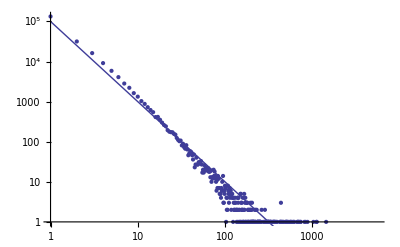

```mathematica
Show[ListLogLogPlot[Tally[cb200[[All,2]]],PlotRange->All],LogLogPlot[10^5/x^2,{x,1,1000}]]
```

```mathematica
hurf2000=ComponentRelabel[ComponentRelabel[ComponentRelabel[ComponentRelabel[ComponentRelabel[cm2000,cmc1,0],4,-3],cmc2,4],cmc3,4],-3,cmc1];
```

```mathematica
hurf2000//Colorize
```

-Graphics-

```mathematica
mm2000=EllsworthMatrix[2000];
cm2000=Componentize[mm2000];
cm2000//Colorize
cb2000=ComponentsByBiggest[cm2000];
{cmc1,cmc2,cmc3}=cb2000[[1;;3,1]];
ComponentSelect[cm2000,cmc1]//Image
ComponentSelect[cm2000,cmc2]//Image
ComponentSelect[cm2000,cmc3]//Image
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

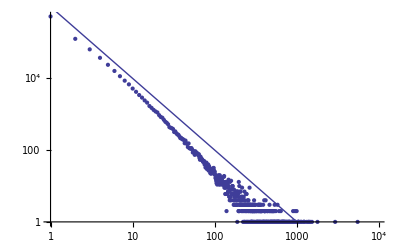

```mathematica
Show[ListLogLogPlot[Tally[cb2000[[All,2]]],PlotRange->All],LogLogPlot[1 10^6/x^2,{x,1,1000}]]
```

```mathematica
cb=ComponentsByBiggest[cm];
```

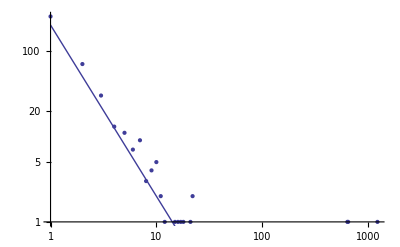

```mathematica
Show[ListLogLogPlot[Tally[cb[[All,2]]],PlotRange->All],LogLogPlot[2 10^2/x^2,{x,1,1000}]]
```

```mathematica
ComponentSelect[cm,7]//Image
ComponentSelect[cm,8]//Image
ComponentSelect[cm,222]//Image
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ComponentsByBiggest[cm]
```

{{222,1229},{8,649},{7,639},{367,22},{106,22},{336,21},{258,18},{278,17},{268,16},{353,15},{329,12},{398,11},{326,11},{382,10},{148,10},{272,10},{58,10},{49,10},{415,9},{152,9},{157,9},{229,9},{43,8},{235,8},{240,8},{368,7},{370,7},{156,7},{362,7},{112,7},{72,7},{259,7},{13,7},{214,7},{394,6},{371,6},{146,6},{301,6},{82,6},{54,6},{29,6},{190,5},{363,5},{139,5},{143,5},{345,5},{302,5},{42,5},{251,5},{23,5},{231,5},{221,5},{413,4},{195,4},{387,4},{161,4},{155,4},{141,4},{121,4},{113,4},{103,4},{85,4},{66,4},{262,4},{232,4},{417,3},{197,3},{196,3},{184,3},{186,3},{380,3},{374,3},{151,3},{347,3},{335,3},{124,3},{320,3},{318,3},{107,3},{312,3},{101,3},{92,3},{84,3},{288,3},{279,3},{69,3},{65,3},{51,3},{48,3},{260,3},{255,3},{247,3},{21,3},{3,3},{215,3},{209,2},{208,2},{412,2},{408,2},{203,2},{199,2},{395,2},{187,2},{183,2},{383,2},{377,2},{176,2},{171,2},{163,2},{369,2},{159,2},{150,2},{359,2},{357,2},{354,2},{144,2},{352,2},{349,2},{138,2},{135,2},{342,2},{131,2},{130,2},{333,2},{332,2},{331,2},{116,2},{324,2},{323,2},{111,2},{110,2},{105,2},{316,2},{104,2},{313,2},{310,2},{309,2},{96,2},{300,2},{296,2},{295,2},{293,2},{87,2},{81,2},{280,2},{68,2},{64,2},{60,2},{266,2},{44,2},{263,2},{256,2},{32,2},{248,2},{244,2},{28,2},{236,2},{19,2},{225,2},{223,2},{220,2},{217,2},{216,2},{2,2},{212,2},{416,1},{210,1},{414,1},{411,1},{410,1},{409,1},{407,1},{207,1},{206,1},{406,1},{205,1},{204,1},{405,1},{404,1},{403,1},{402,1},{401,1},{202,1},{400,1},{399,1},{201,1},{200,1},{198,1},{397,1},{396,1},{393,1},{194,1},{193,1},{192,1},{191,1},{392,1},{391,1},{390,1},{389,1},{388,1},{189,1},{188,1},{185,1},{386,1},{385,1},{384,1},{182,1},{181,1},{180,1},{381,1},{379,1},{378,1},{179,1},{178,1},{177,1},{175,1},{174,1},{173,1},{172,1},{376,1},{375,1},{170,1},{169,1},{168,1},{167,1},{166,1},{373,1},{372,1},{165,1},{164,1},{162,1},{160,1},{366,1},{365,1},{158,1},{364,1},{154,1},{153,1},{361,1},{149,1},{360,1},{358,1},{147,1},{356,1},{355,1},{145,1},{142,1},{351,1},{350,1},{348,1},{140,1},{346,1},{137,1},{136,1},{134,1},{344,1},{343,1},{341,1},{340,1},{133,1},{132,1},{339,1},{338,1},{337,1},{129,1},{128,1},{127,1},{126,1},{125,1},{334,1},{123,1},{122,1},{330,1},{120,1},{119,1},{118,1},{328,1},{327,1},{117,1},{115,1},{114,1},{325,1},{322,1},{321,1},{109,1},{319,1},{108,1},{317,1},{315,1},{314,1},{311,1},{102,1},{308,1},{100,1},{99,1},{307,1},{306,1},{305,1},{304,1},{303,1},{98,1},{97,1},{95,1},{94,1},{93,1},{299,1},{298,1},{297,1},{91,1},{90,1},{294,1},{292,1},{89,1},{88,1},{291,1},{290,1},{86,1},{289,1},{83,1},{80,1},{79,1},{78,1},{77,1},{287,1},{286,1},{285,1},{284,1},{283,1},{282,1},{76,1},{281,1},{75,1},{74,1},{73,1},{71,1},{70,1},{67,1},{277,1},{276,1},{275,1},{274,1},{273,1},{63,1},{62,1},{61,1},{271,1},{270,1},{269,1},{59,1},{57,1},{56,1},{55,1},{53,1},{52,1},{267,1},{265,1},{50,1},{47,1},{264,1},{46,1},{45,1},{261,1},{41,1},{40,1},{39,1},{38,1},{257,1},{254,1},{37,1},{36,1},{253,1},{35,1},{34,1},{33,1},{31,1},{252,1},{250,1},{249,1},{246,1},{245,1},{30,1},{243,1},{242,1},{241,1},{27,1},{26,1},{25,1},{24,1},{239,1},{238,1},{237,1},{234,1},{22,1},{20,1},{233,1},{230,1},{18,1},{17,1},{16,1},{15,1},{228,1},{14,1},{227,1},{226,1},{224,1},{12,1},{11,1},{10,1},{9,1},{219,1},{218,1},{6,1},{5,1},{4,1},{1,1},{213,1},{211,1}}

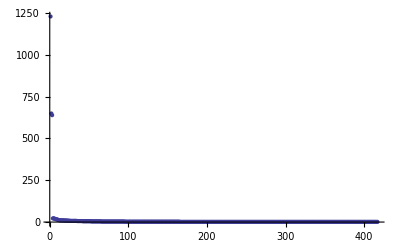

```mathematica
ListPlot[ComponentsByBiggest[cm][[All,2]],PlotRange->All]
```

```mathematica
SortSecond[Tally[Flatten[bb+a]]]
```

{{1126,7066},{35,3450},{1,3358},{594,180},{810,110},{1899,81},{1116,70},{1186,69},{1342,63},{555,59},{1607,53},{1988,51},{608,45},{421,41},{194,38},{1502,33},{429,32},{133,31},{756,29},{1529,27},{642,25},{1473,25},{304,24},{68,24},{473,23},«2160»,{1124,1},{1123,1},{1122,1},{1121,1},{1120,1},{1118,1},{15,1},{14,1},{13,1},{12,1},{11,1},{1113,1},{1111,1},{1106,1},{1105,1},{1104,1},{1102,1},{10,1},{9,1},{1100,1},{7,1},{5,1},{1098,1},{1094,1}}

```mathematica
N[7066/19900]
```

0.355075